# Gradient Flow and Closest Normal Matrices

The goal in this notebook is to perform the numerical experiments reported in “Geometry of normal matrices,” by Tom Needham and Clayton Shonkwiler. This work was supported by the National Science Foundation (DMS–2107808 and DMS–2107700).

Specifically, the goal is, for various complex and real random starting matrices, to compare the distance to the closest normal matrix with the distance to the limit of negative gradient flow of the non-normal energy defined in the paper.

## Ruhe’s algorithm

First, we give an implementation of Ruhe's algorithm for computing the closest normal matrix to a given matrix. The following is my intepretation of Algorithm J in Ruhe’s paper; notice that, as Higham points out, the published version of Algorithm J is missing a minus sign before the determinant in the definition of the angle .

```mathematica
RuheIteration[{A_,R_}]:=Module[{j,k,n,block,m,θ,h,ϕ,α,newR},
If[SquareMatrixQ[A],n=Length[A];,Print["Input isn't a square matrix!"]; Abort[]];
{j,k}=Sort[RandomSample[Range[n],2]];
block=A[[{j,k},{j,k}]];
m=Tr[block]/2;
θ=1/2 Arg[-Det[block-m*IdentityMatrix[2]]];
h=E^(-I θ)A[[j,k]]+E^(I θ)Conjugate[A[[k,j]]];
ϕ=If[Abs[θ]==π/2,If[h==0,0,π/4],1/2 ArcTan[Abs[h]/Re[E^(-I θ)(A[[j,j]]-A[[k,k]])]]];
α=Arg[h];
newR=SparseArray[Join[{{j,j}->Cos[ϕ],{j,k}->-E^(I α)Sin[ϕ],{k,j}->E^(-I α)Sin[ϕ],{k,k}->Cos[ϕ]},Table[{i,i}->1,{i,Complement[Range[n],{j,k}]}]],{n,n}];
{ConjugateTranspose[newR].A.newR,R.newR}
];
```

```mathematica
RuheAlgorithm[A_]:=Module[{newA,R},
If[!SquareMatrixQ[A],Print["Input isn't a square matrix!"]; Abort[]];
{newA,R}=Nest[RuheIteration,{A,IdentityMatrix[Length[A]]},10000];
R.DiagonalMatrix[Diagonal[newA]].ConjugateTranspose[R]
];
```

## Unconstrained optimization

First, we compare to the gradient descent of E, which does not preserve Frobenius norms. To keep things on a level footing, we initialize our starting matrices to always have Frobenius norm 1.

### Complex matrices

Here, we’ll start with complex  matrices which are normalizations of matrices with standard Gaussians in each entry. For each of 10,000 random starting matrices, we’ll compute the squared distance to the closest normal matrix and the squared distance to the limit of gradient descent.

```mathematica
data20x20normalized=Module[{A,flow,closest,ϵ=.01},
ParallelTable[
A=#/Norm[#,"Frobenius"]&[RandomVariate[NormalDistribution[],{20,20}]+I*RandomVariate[NormalDistribution[],{20,20}]];
closest=RuheAlgorithm[A];
flow=FixedPoint[(#-ϵ ((#.ConjugateTranspose[#]-ConjugateTranspose[#].#).#-#.(#.ConjugateTranspose[#]-ConjugateTranspose[#].#)))&,A,10000];
{Norm[A-closest,"Frobenius"]^2,Norm[A-flow,"Frobenius"]^2},{10000}]
];
```

And then plot the points with these two distances as its  and  coordinates. All points should be above the line :

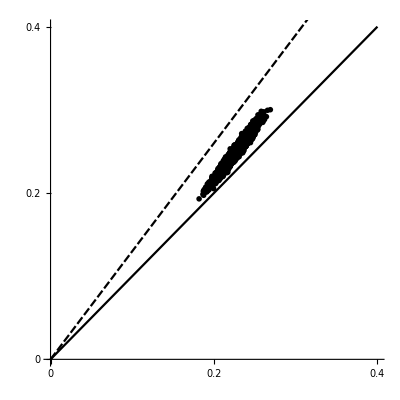

```mathematica
flow1=With[{max=Max[Flatten[data20x20normalized]]+.1},Show[ListPlot[data20x20normalized,PlotTheme->"Monochrome",PlotRange->{{0,max},{0,max}},AspectRatio->1,Ticks->{{0,.2,.4},{0,.2,.4}},TicksStyle->Directive[FontFamily->"Latin Modern Math", 24],AxesStyle->Directive[Black,Thickness[.005]]],Plot[{x,1.3x},{x,0,max},PlotTheme->"Monochrome"]]
]
```

Find the interval that the ratios live in:

```mathematica
MinMax[(#[[2]])/(#[[1]])&/@data20x20normalized]
```

{1.0282,1.16052}

```mathematica
Export[NotebookDirectory[]<>"flow1.pdf",flow1];
```

```mathematica
NotebookSave[]
```

### Real matrices

Now we do the same, but make all the initial matrices be real:

```mathematica
data20x20normalizedreal=Module[{A,flow,closest,ϵ=.01},
ParallelTable[
A=#/Norm[#,"Frobenius"]&[RandomVariate[NormalDistribution[],{20,20}]];
closest=RuheAlgorithm[A];
flow=FixedPoint[(#-ϵ ((#.ConjugateTranspose[#]-ConjugateTranspose[#].#).#-#.(#.ConjugateTranspose[#]-ConjugateTranspose[#].#)))&,A,10000];
{Norm[A-closest,"Frobenius"]^2,Norm[A-flow,"Frobenius"]^2},{10000}]
];
```

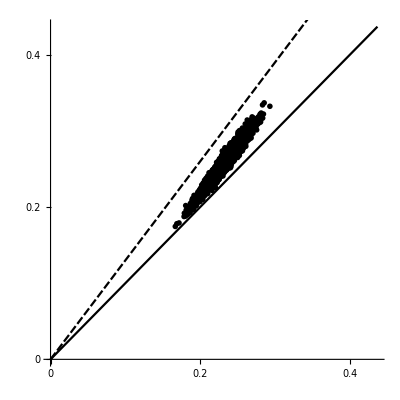

```mathematica
flow2=With[{max=Max[Flatten[data20x20normalizedreal]]+.1},Show[ListPlot[data20x20normalizedreal,PlotTheme->"Monochrome",PlotRange->{{0,max},{0,max}},AspectRatio->1,Ticks->{{0,.2,.4},{0,.2,.4}},TicksStyle->Directive[FontFamily->"Latin Modern Math", 24],AxesStyle->Directive[Black,Thickness[.005]]],Plot[{x,1.3x},{x,0,max},PlotTheme->"Monochrome"]]
]
```

```mathematica
MinMax[(#[[2]])/(#[[1]])&/@data20x20normalizedreal]
```

{1.02311,1.1958}

```mathematica
Export[NotebookDirectory[]<>"flow2.pdf",flow2];
```

```mathematica
NotebookSave[]
```

### Nearly-normal matrices

Now we choose initial matrices which are already nearly normal. To do so, we’ll start with normalized random complex matrices as before, find the closest normal matrix, perturb each entry by a small Gaussian, and then renormalize to get the starting point for gradient flow.

```mathematica
data20x20normalizedclose=Module[{B,start,flow,closest,ϵ=1,var=.0075},
ParallelTable[
B=#/Norm[#,"Frobenius"]&[RandomVariate[NormalDistribution[],{20,20}]+I*RandomVariate[NormalDistribution[],{20,20}]];
start=#/Norm[#,"Frobenius"]&[RuheAlgorithm[B]+RandomVariate[NormalDistribution[0,var],{20,20}]+I*RandomVariate[NormalDistribution[0,var],{20,20}]];
closest=RuheAlgorithm[start];
flow=FixedPoint[(#-ϵ ((#.ConjugateTranspose[#]-ConjugateTranspose[#].#).#-#.(#.ConjugateTranspose[#]-ConjugateTranspose[#].#)))&,start,100000];
{Norm[start-closest,"Frobenius"]^2,Norm[start-flow,"Frobenius"]^2},{10000}]
];
```

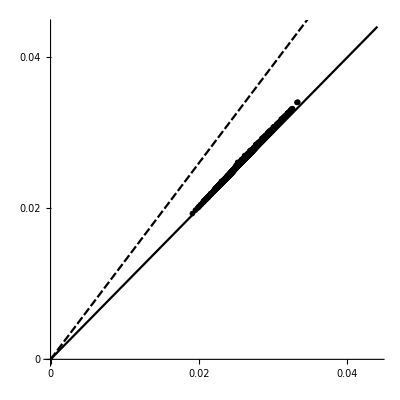

```mathematica
flow3=With[{max=Max[Flatten[data20x20normalizedclose]]+.01},Show[ListPlot[data20x20normalizedclose,PlotTheme->"Monochrome",PlotRange->{{0,max},{0,max}},AspectRatio->1,Ticks->{{0,.02,.04},{0,.02,.04}},TicksStyle->Directive[FontFamily->"Latin Modern Math", 24],AxesStyle->Directive[Black,Thickness[.005]]],Plot[{x,1.3x},{x,0,max},PlotTheme->"Monochrome"]]
]
```

```mathematica
MinMax[(#[[2]])/(#[[1]])&/@data20x20normalizedclose]
```

{1.00996,1.03501}

```mathematica
Export[NotebookDirectory[]<>"flow3.pdf",flow3];
```

```mathematica
NotebookSave[]
```

## Constrained optimization

Now, we will run the same experiments, but by gradient descent of the energy function , which preserves Frobenius norm. Other than this change, all computations are exactly the same as before.

### Complex matrices

```mathematica
data20x20fixed=Module[{A,flow,closest,ϵ=.01},
ParallelTable[
A=#/Norm[#,"Frobenius"]&[RandomVariate[NormalDistribution[],{20,20}]+I*RandomVariate[NormalDistribution[],{20,20}]];
closest=RuheAlgorithm[A];
flow=FixedPoint[(#-ϵ ((#.ConjugateTranspose[#]-ConjugateTranspose[#].#).#-#.(#.ConjugateTranspose[#]-ConjugateTranspose[#].#)-Norm[#.ConjugateTranspose[#]-ConjugateTranspose[#].#,"Frobenius"]^2#))&,A,10000];
{Norm[A-closest,"Frobenius"]^2,Norm[A-flow,"Frobenius"]^2},{10000}]
];
```

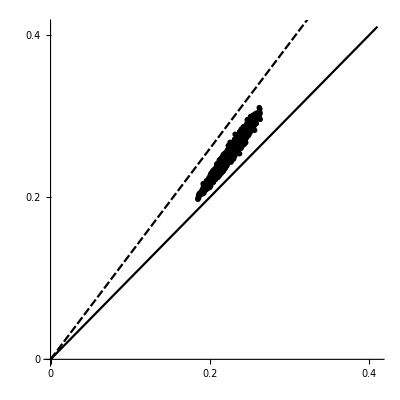

```mathematica
rflow1=With[{max=Max[Flatten[data20x20fixed]]+.1},Show[ListPlot[data20x20fixed,PlotTheme->"Monochrome",PlotRange->{{0,max},{0,max}},AspectRatio->1,Ticks->{{0,.2,.4},{0,.2,.4}},TicksStyle->Directive[FontFamily->"Latin Modern Math", 24],AxesStyle->Directive[Black,Thickness[.005]]],Plot[{x,1.3x},{x,0,max},PlotTheme->"Monochrome"]]
]
```

```mathematica
MinMax[(#[[2]])/(#[[1]])&/@data20x20fixed]
```

{1.06089,1.19776}

```mathematica
Export[NotebookDirectory[]<>"rflow1.pdf",rflow1];
```

```mathematica
NotebookSave[]
```

### Real matrices

```mathematica
data20x20fixedreal=Module[{A,flow,closest,ϵ=.01},
ParallelTable[
A=#/Norm[#,"Frobenius"]&[RandomVariate[NormalDistribution[],{20,20}]];
closest=RuheAlgorithm[A];
flow=FixedPoint[(#-ϵ ((#.ConjugateTranspose[#]-ConjugateTranspose[#].#).#-#.(#.ConjugateTranspose[#]-ConjugateTranspose[#].#)-Norm[#.ConjugateTranspose[#]-ConjugateTranspose[#].#,"Frobenius"]^2#))&,A,10000];
{Norm[A-closest,"Frobenius"]^2,Norm[A-flow,"Frobenius"]^2},{10000}]
];
```

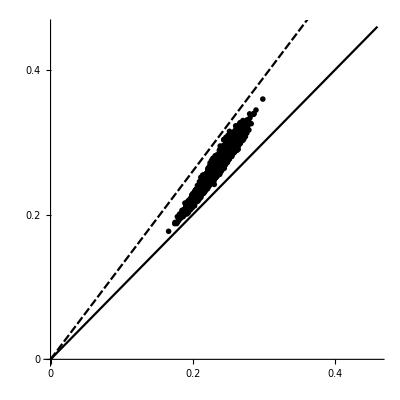

```mathematica
rflow2=With[{max=Max[Flatten[data20x20fixedreal]]+.1},Show[ListPlot[data20x20fixedreal,PlotTheme->"Monochrome",PlotRange->{{0,max},{0,max}},AspectRatio->1,Ticks->{{0,.2,.4},{0,.2,.4}},TicksStyle->Directive[FontFamily->"Latin Modern Math", 24],AxesStyle->Directive[Black,Thickness[.005]]],Plot[{x,1.3x},{x,0,max},PlotTheme->"Monochrome"]]
]
```

```mathematica
MinMax[(#[[2]])/(#[[1]])&/@data20x20fixedreal]
```

{1.04607,1.25214}

```mathematica
Export[NotebookDirectory[]<>"rflow2.pdf",rflow2];
```

```mathematica
NotebookSave[]
```

### Nearly-normal matrices

```mathematica
data20x20fixedclose=Module[{B,start,flow,closest,ϵ=1,var=.0075},
ParallelTable[
B=#/Norm[#,"Frobenius"]&[RandomVariate[NormalDistribution[],{20,20}]+I*RandomVariate[NormalDistribution[],{20,20}]];
start=#/Norm[#,"Frobenius"]&[RuheAlgorithm[B]+RandomVariate[NormalDistribution[0,var],{20,20}]+I*RandomVariate[NormalDistribution[0,var],{20,20}]];
closest=RuheAlgorithm[start];
flow=FixedPoint[(#-ϵ ((#.ConjugateTranspose[#]-ConjugateTranspose[#].#).#-#.(#.ConjugateTranspose[#]-ConjugateTranspose[#].#)-Norm[#.ConjugateTranspose[#]-ConjugateTranspose[#].#,"Frobenius"]^2#))&,start,100000];
{Norm[start-closest,"Frobenius"]^2,Norm[start-flow,"Frobenius"]^2},{100000}]
];
```

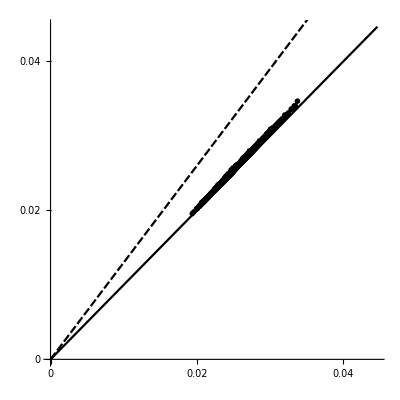

```mathematica
rflow3=With[{max=Max[Flatten[data20x20fixedclose[[;;10000]]]]+.01},Show[ListPlot[data20x20fixedclose[[;;10000]],PlotTheme->"Monochrome",PlotRange->{{0,max},{0,max}},AspectRatio->1,Ticks->{{0,.02,.04},{0,.02,.04}},TicksStyle->Directive[FontFamily->"Latin Modern Math", 24],AxesStyle->Directive[Black,Thickness[.005]]],Plot[{x,1.3x},{x,0,max},PlotTheme->"Monochrome"]]
]
```

```mathematica
MinMax[(#[[2]])/(#[[1]])&/@data20x20fixedclose[[;;10000]]]
```

{1.01023,1.03077}

```mathematica
Export[NotebookDirectory[]<>"rflow3.pdf",rflow3];
```

```mathematica
NotebookSave[]
```